Gráfico salvo na área de trabalho como:

C:\Users\DELL\Desktop\PontosLagrange_Yukawa_TCC.pdf

C:\Users\DELL\Desktop\PontosLagrange_Yukawa_TCC.png

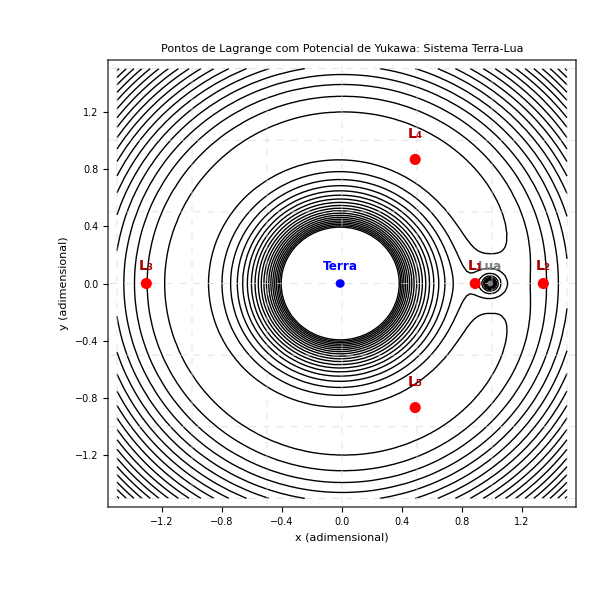

```mathematica
(*Parâmetros do sistema Terra-Lua com alta precisão*)EarthMass=5.97219`30*10^24;    (*kg*)
MoonMass=7.34767309`30*10^22;  (*kg*)
alphaMass=MoonMass/(EarthMass+MoonMass);
alphaYuk=0.1`30;  (*Parâmetro Yukawa*)
lambda=1.0`30;    (*Alcance adimensional*)

(*Definir todas as funções com precisão estendida*)
d1[x_,y_]:=Sqrt[(x+alphaMass)^2+y^2];
d2[x_,y_]:=Sqrt[(x-(1-alphaMass))^2+y^2];
q1[x_,y_]:=1+alphaYuk*Exp[-lambda*d1[x,y]];
q2[x_,y_]:=1+alphaYuk*Exp[-lambda*d2[x,y]];
k=1+alphaYuk*(1+lambda)*Exp[-lambda];

(*Potencial efetivo com Yukawa*)
UYukawa[x_,y_]:=-((1-alphaMass)/d1[x,y])*q1[x,y]-(alphaMass/d2[x,y])*q2[x,y]-(1/2)*(x^2+y^2);

(*Funções auxiliares para FindRoot com precisão*)
eqL1[x_?NumericQ]:=Module[{r1=d1[x,0],r2=d2[x,0]},x-(1-alphaMass)/k*(x+alphaMass)/r1^3*q1[x,0]*(1+lambda*r1)-alphaMass/k*(x-(1-alphaMass))/r2^3*q2[x,0]*(1+lambda*r2)];

eqL2[x_?NumericQ]:=Module[{r1=d1[x,0],r2=d2[x,0]},x-(1-alphaMass)/k*(x+alphaMass)/r1^3*q1[x,0]*(1+lambda*r1)-alphaMass/k*(x-(1-alphaMass))/r2^3*q2[x,0]*(1+lambda*r2)];

eqL3[x_?NumericQ]:=Module[{r1=d1[x,0],r2=d2[x,0]},x-(1-alphaMass)/k*(x+alphaMass)/r1^3*q1[x,0]*(1+lambda*r1)-alphaMass/k*(x-(1-alphaMass))/r2^3*q2[x,0]*(1+lambda*r2)];

(*Cálculo dos pontos de Lagrange com Yukawa*)
L1Solution=FindRoot[eqL1[x]==0,{x,1-alphaMass-0.1},WorkingPrecision->30,MaxIterations->1000];
L2Solution=FindRoot[eqL2[x]==0,{x,1-alphaMass+0.1},WorkingPrecision->30,MaxIterations->1000];
L3Solution=FindRoot[eqL3[x]==0,{x,-alphaMass-1},WorkingPrecision->30,MaxIterations->1000];

(*Pontos de Lagrange*)
LagrangePoints={{"L₁",{x/. L1Solution,0}},{"L₂",{x/. L2Solution,0}},{"L₃",{x/. L3Solution,0}},{"L₄",{1/2-alphaMass,Sqrt[3]/2}},{"L₅",{1/2-alphaMass,-Sqrt[3]/2}}};

(*Gráfico profissional*)
lagrangePlot=Show[ContourPlot[UYukawa[x,y],{x,-1.5,1.5},{y,-1.5,1.5},Contours->20,ContourShading->None,ContourStyle->Directive[Black,Thin],PlotRange->{{-1.5,1.5},{-1.5,1.5}}],Graphics[{{Blue,Disk[{-alphaMass,0},0.03],Text[Style["Terra",12,Bold,FontFamily->"Times"],{-alphaMass,0.12}]},{Gray,Disk[{1-alphaMass,0},0.02],Text[Style["Lua",12,Bold,FontFamily->"Times"],{1-alphaMass,0.12}]},{Red,AbsolutePointSize[8],Point[#[[2]]&/@LagrangePoints]},MapThread[Text[Style[#1,14,Bold,Darker[Red],FontFamily->"Times"],{#2[[1]],#2[[2]]+If[#2[[2]]==0,0.12,0.18]}]&,{First/@LagrangePoints,Last/@LagrangePoints}]}],Frame->True,FrameLabel->{Style["x (adimensional)",14,FontFamily->"Times"],Style["y (adimensional)",14,FontFamily->"Times"]},PlotLabel->Style["Pontos de Lagrange com Potencial de Yukawa: Sistema Terra-Lua",16,Bold,FontFamily->"Times"],GridLines->{Range[-1.5,1.5,0.5],Range[-1.5,1.5,0.5]},GridLinesStyle->Directive[LightGray,Dashed],ImageSize->600,AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->12},FrameStyle->Directive[Black,Thick]];

(*Exportar gráficos*)
desktopPath=FileNameJoin[{$HomeDirectory,"Desktop"}];
Export[FileNameJoin[{desktopPath,"PontosLagrange_Yukawa_TCC.pdf"}],lagrangePlot,ImageResolution->600];
Export[FileNameJoin[{desktopPath,"PontosLagrange_Yukawa_TCC.png"}],lagrangePlot,ImageResolution->300];

(*Exibir o gráfico*)
Print["Gráfico salvo na área de trabalho como:"];
Print[FileNameJoin[{desktopPath,"PontosLagrange_Yukawa_TCC.pdf"}]];
Print[FileNameJoin[{desktopPath,"PontosLagrange_Yukawa_TCC.png"}]];

lagrangePlot
```